# Projet Final de IFT6390 Algorithme de Réseau à convolution

## Professeur : Aaron Courville Étudiants: Zhibin Lu, Léa-Marie Normandin et Xiaocheng Liu 1. Sur MNIST Pour les données de MNIST, on va constater l’influence sur les hyper-paramètres traditionnels (Taux d’apprentissage, batchsize, régularisation) en fixant la taille de neurones couches cachées :

```mathematica
mtrainset=ExampleData[{"MachineLearning","MNIST"},"TrainingData"];
mtestset=ExampleData[{"MachineLearning","MNIST"},"TestData"];
```

```mathematica
indexs=Table[i,{i,1,Length[mtrainset]}];
indexs=RandomSample[indexs];
mvalidset=mtrainset[[indexs[[1;;10000]]]];
mtrainset=mtrainset[[indexs[[10001;;50000]]]];
```

-Graphics-

```mathematica
mCNNChain=NetChain[{
ConvolutionLayer[20,{5,5}],
ElementwiseLayer[Ramp], 
PoolingLayer[{2,2},{2,2}], 
ConvolutionLayer[50,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
LinearLayer[400], 
ElementwiseLayer[Ramp],
LinearLayer[10],
SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",Range[0,9]}],
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]
]
```

NetChain[]

```mathematica
mCNNtrained0=NetTrain[mCNNChain,mtrainset,ValidationSet->mvalidset,MaxTrainingRounds->5]
ClassifierMeasurements[mCNNtrained0,mtestset,{"Error"}][[1]]
```

NetChain[]

0.0101

```mathematica
(*mCNNtrained1=NetTrain[mCNNChain,mtrainset,ValidationSet->mvalidset,MaxTrainingRounds->5]*)
(*NetTrain[mCNNChain,mtrainset,ValidationSet->mvalidset,MaxTrainingRounds-> 5,BatchSize->500,Method->{"SGD","L2Regularization"->0.00001},*)

(*Pour les donnees de MNIST,on va constater L’influence sur les hyper-parametres traditionnels (Taux d’apprentissage,batchsize,regularisation) en fixant la taille de neurones couches cachees *)
errset={};
Do[
mCNNtrained=NetTrain[mCNNChain,mtrainset,ValidationSet->mvalidset,MaxTrainingRounds-> 5,BatchSize->50,Method->{"SGD","L2Regularization"->0.0},LearningRateMultipliers->{_->3}];

errset=Append[errset,ClassifierMeasurements[mCNNtrained,mtestset,{"Error"}][[1]]];

,3]
Print[errset];
```

{0.0101,0.0104,0.0097}

```mathematica
(*pour l'hyper-parametre de regularisation*)
errtrain={};
errvalid={};
errtest={};
mCNNtrained= mCNNChain;
Do[
mCNNtrained=NetTrain[mCNNtrained,mtrainset,MaxTrainingRounds-> 1,BatchSize->100,Method->{"SGD","L2Regularization"->0.000000000001},LearningRateMultipliers->{_->1.8}];
err1=ClassifierMeasurements[mCNNtrained,mtrainset,{"Error"}][[1]];
errtrain=Append[errtrain,err1];
err2=ClassifierMeasurements[mCNNtrained,mvalidset,{"Error"}][[1]];
errvalid=Append[errvalid,err2];
err3=ClassifierMeasurements[mCNNtrained,mtestset,{"Error"}][[1]];
errtest=Append[errtest,err3];

,30];
```

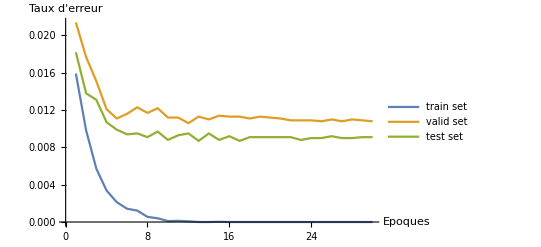

```mathematica
(*grande variance*)
merrset1={errtrain,errvalid,errtest};
ListLinePlot[{errtrain,errvalid,errtest},AxesLabel->{"Epoques","Taux d'erreur"},PlotLegends->{"train set","valid set","test set"}]
```

```mathematica
errtest
```

{0.0182,0.0138,0.0131,0.0107,0.0099,0.0094,0.0095,0.0091,0.0097,0.0088,0.0093,0.0095,0.0087,0.0095,0.0088,0.0092,0.0087,0.0091,0.0091,0.0091,0.0091,0.0091,0.0088,0.009,0.009,0.0092,0.009,0.009,0.0091,0.0091}

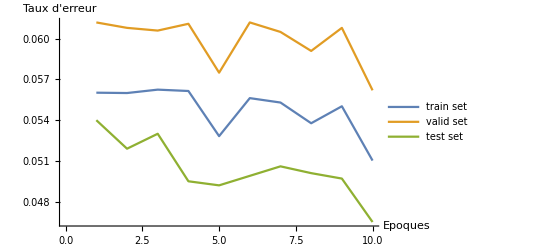

```mathematica
errtrain2={};
errvalid2={};
errtest2={};
mCNNtrained= mCNNChain;
Do[
mCNNtrained=NetTrain[mCNNtrained,mtrainset,MaxTrainingRounds-> 1,BatchSize->100,Method->{"SGD","L2Regularization"->0.05},LearningRateMultipliers->{_->1.8}];
err1=ClassifierMeasurements[mCNNtrained,mtrainset,{"Error"}][[1]];
errtrain2=Append[errtrain2,err1];
err2=ClassifierMeasurements[mCNNtrained,mvalidset,{"Error"}][[1]];
errvalid2=Append[errvalid2,err2];
err3=ClassifierMeasurements[mCNNtrained,mtestset,{"Error"}][[1]];
errtest2=Append[errtest2,err3];

,10];

(*grand biais*)
merrset2={errtrain2,errvalid2,errtest2};
ListLinePlot[{errtrain2,errvalid2,errtest2},AxesLabel->{"Epoques","Taux d'erreur"},PlotLegends->{"train set","valid set","test set"}]
```

```mathematica
(*le bon choix*)
errtrain3={};
errvalid3={};
errtest3={};
mCNNtrained= mCNNChain;
Do[
mCNNtrained=NetTrain[mCNNtrained,mtrainset,MaxTrainingRounds-> 1,BatchSize->240,Method->{"SGD","L2Regularization"->0.000001},LearningRateMultipliers->{_->1.7}];
err1=ClassifierMeasurements[mCNNtrained,mtrainset,{"Error"}][[1]];
errtrain3=Append[errtrain3,err1];
err2=ClassifierMeasurements[mCNNtrained,mvalidset,{"Error"}][[1]];
errvalid3=Append[errvalid3,err2];
err3=ClassifierMeasurements[mCNNtrained,mtestset,{"Error"}][[1]];
errtest3=Append[errtest3,err3];
If[err3<0.0099,Break[]];

,30];
```

Taux d'erreur sur test:0.0098

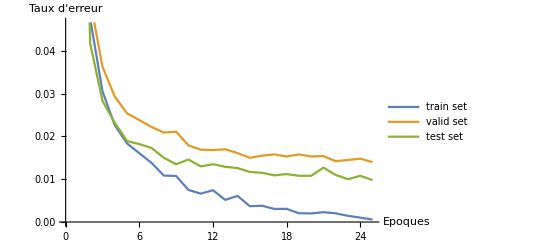

```mathematica
(*la bonne courbe*)
Print["Taux d'erreur sur test:",err3]
merrset3={errtrain3,errvalid3,errtest3};
ListLinePlot[{errtrain3,errvalid3,errtest3},AxesLabel->{"Epoques","Taux d'erreur"},PlotLegends->{"train set","valid set","test set"}]
```

## Conclusion : 1. On conseille d’essayer quelques valeurs sur certains de hyper-paramètres en fixant les autres hyper-paramètres pour obtenir des expériences sur la question réelle. Étant donné que le nombre d’hyper-paramètres est élevé, l’exécution du programme peut prendre beaucoup de temps. Il est conseillé d’y aller par combinaison d’hyper-paramètres. 2. Si on a un ensemble de données assez grand, on peut entraîner un modèle avec une plus grande capacité sans avoir peur d’être dans une situation de sur-apprentissage.

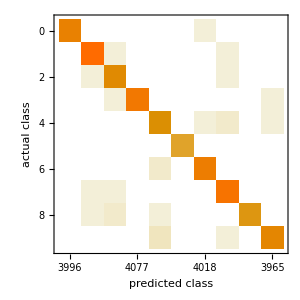
{0.000575,-Graphics-}

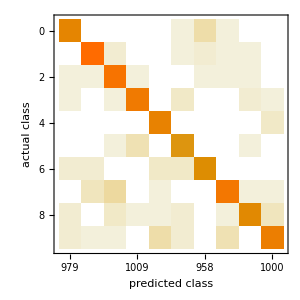
{0.0098,-Graphics-}

```mathematica
ClassifierMeasurements[mCNNtrained,mtrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[mCNNtrained,mtestset,{"Error","ConfusionMatrixPlot"}]
```

```mathematica
(*"Est - ce que les examples " difficiles " et " faciles " d' une base de données sont les mêmes pour tous les algorithmes choisis?"*)
mimages=Keys[mtestset];
mentropies=mCNNtrained[mimages,"Entropy"];
(*choisir les images qui ont le plus haut d'entropie*)
mimages[[Ordering[mentropies,-30]]] 
(*choisir les images qui ont le plus bas d'entropie*)
mimages[[Ordering[mentropies,30]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 2. CIFAR - 10 Pour les données de CIFAR-10, on va constater l’influence sur les hyper-paramètres de couche neurone (taille de filtre et taille de pooling) en fixant les autres hyper-paramètres. Les autres hyper-paramètres sont comme : époque = 10~20, mini BatchSize = 200~300, Regularization= 0.0000001, Taux d’apprentissage de descente gradient = 2.4, deux couche de Multi-layer Perceptron(800 neurones et 100 neurones) pour la sortie.

```mathematica
obj=ResourceObject["CIFAR-10"]
ctrainset=ResourceData[obj,"TrainingData"];
ctestset=ResourceData[obj,"TestData"];
indexs=Table[i,{i,1,Length[ctrainset]}];
indexs=RandomSample[indexs];
cvalidset=ctrainset[[indexs[[1;;10000]]]];
ctrainset=ctrainset[[indexs[[10001;;50000]]]];
```

ResourceObject[…]

```mathematica
ResourceObject[…]
```

```mathematica
cCNNchain1=NetChain[{
ConvolutionLayer[30,{5,5}], (* Filtres de noyau à convolution *)
ElementwiseLayer[Ramp],(* Function d'activation ReLU *)
PoolingLayer[{2,2},{2,2}], (* Pooling filtres *)
FlattenLayer[],
LinearLayer[800], (* Multi-Layer Perceptron *)
ElementwiseLayer[Ramp],
LinearLayer[100], (* Deuxieme Multi-Layer Perceptron *)
ElementwiseLayer[Ramp],
LinearLayer[10],
SoftmaxLayer[]}, (*Function d'activation pour la sortie *)
"Output"->NetDecoder[{"Class",{"ship","airplane","automobile","bird","cat","deer","dog","frog","horse","truck"}}],
"Input"->NetEncoder[{"Image",{32,32},"RGB"}]
]


errtrain21={};
errvalid21={};
errtest21={};
cCNNtrained1= cCNNchain1;
For[i=1,i≤15,i++,
Print["Epouqe",i];
cCNNtrained1=NetTrain[cCNNtrained1,ctrainset,MaxTrainingRounds-> 1,BatchSize->300,Method->{"SGD","L2Regularization"->0.0000001},LearningRateMultipliers->{_->2.4}];
err1=ClassifierMeasurements[cCNNtrained1,ctrainset,{"Error"}][[1]];
errtrain21=Append[errtrain21,err1];
err2=ClassifierMeasurements[cCNNtrained1,cvalidset,{"Error"}][[1]];
errvalid21=Append[errvalid21,err2];
err3=ClassifierMeasurements[cCNNtrained1,ctestset,{"Error"}][[1]];
errtest21=Append[errtest21,err3];
Print["Taux ",err1," ",err2," ",err3];
If[err3<0.3,Break[]];
];
```

NetChain[]

Epouqe1

Taux 0.891425 0.8915 0.8914

Epouqe2

Taux 0.73515 0.741 0.7423

Epouqe3

Taux 0.59265 0.6038 0.6013

Epouqe4

Taux 0.53555 0.5617 0.5552

Epouqe5

Taux 0.487225 0.5276 0.5236

Epouqe6

Taux 0.430725 0.5023 0.4903

Epouqe7

Taux 0.396725 0.4925 0.4801

Epouqe8

Taux 0.3368 0.4699 0.4619

Epouqe9

Taux 0.308375 0.471 0.4654

Epouqe10

Taux 0.258625 0.4582 0.4588

Epouqe11

Taux 0.22885 0.4703 0.4644

Epouqe12

Taux d'erreur sur test:0.4644

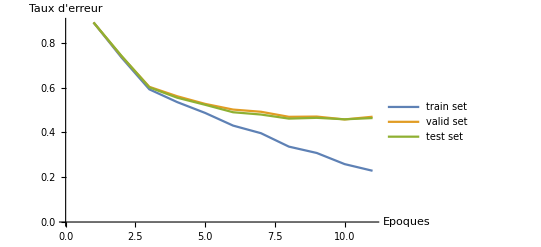

```mathematica
Print["Taux d'erreur sur test:",err3]
cerrset1={errtrain21,errvalid21,errtest21};
ListLinePlot[{errtrain21,errvalid21,errtest21},AxesLabel->{"Epoques","Taux d'erreur"},PlotLegends->{"train set","valid set","test set"}]
```

-Graphics--Graphics-

```mathematica
cCNNchain2=NetChain[{
ConvolutionLayer[30,{9,9}],(* Permiere couche, Filtres de noyau à convolution *)
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}], 
ConvolutionLayer[90,{9,9}],(* Deuxieme couche ,Filtres de noyau à convolution *)
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}], 
FlattenLayer[],
LinearLayer[800], 
ElementwiseLayer[Ramp],
LinearLayer[100],
ElementwiseLayer[Ramp],
LinearLayer[10],
SoftmaxLayer[]}, 
"Output"->NetDecoder[{"Class",{"ship","airplane","automobile","bird","cat","deer","dog","frog","horse","truck"}}],
"Input"->NetEncoder[{"Image",{32,32},"RGB"}]
]


errtrain22={};
errvalid22={};
errtest22={};
cCNNtrained2= cCNNchain2;
For[i=1,i≤15,i++,
Print["Epouqe",i];
cCNNtrained2=NetTrain[cCNNtrained2,ctrainset,MaxTrainingRounds-> 1,BatchSize->300,Method->{"SGD","L2Regularization"->0.0000001},LearningRateMultipliers->{_->2.4}];
err1=ClassifierMeasurements[cCNNtrained2,ctrainset,{"Error"}][[1]];
errtrain22=Append[errtrain22,err1];
err2=ClassifierMeasurements[cCNNtrained2,cvalidset,{"Error"}][[1]];
errvalid22=Append[errvalid22,err2];
err3=ClassifierMeasurements[cCNNtrained2,ctestset,{"Error"}][[1]];
errtest22=Append[errtest22,err3];
Print["Taux ",err1," ",err2," ",err3];
If[err3<0.4,Break[]];
];
```

NetChain[]

Epouqe1

Taux 0.873825 0.879 0.8759

Epouqe2

Taux 0.89985 0.9004 0.9

Epouqe3

Taux 0.898325 0.8993 0.8991

Epouqe4

Taux 0.8999 0.9001 0.9001

Epouqe5

Taux 0.899225 0.8998 0.9001

Epouqe6

Taux 0.858675 0.8631 0.8615

Epouqe7

Taux 0.898975 0.9042 0.8999

Epouqe8

Taux 0.899925 0.8997 0.9004

Epouqe9

Taux 0.898925 0.9042 0.9

Epouqe10

Taux 0.899925 0.9003 0.9

Epouqe11

Taux 0.900575 0.8964 0.9003

Epouqe12

Taux 0.895025 0.8998 0.8966

Epouqe13

Taux 0.897625 0.8993 0.8986

Epouqe14

Taux 0.8985 0.9028 0.8998

Epouqe15

Taux 0.8993 0.9004 0.8988

Taux d'erreur sur test:0.8988

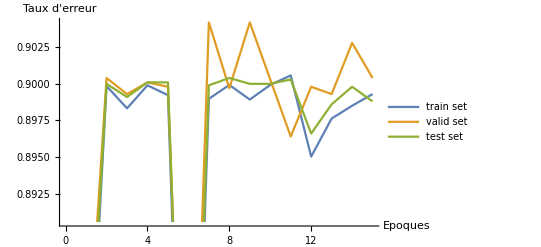

```mathematica
Print["Taux d'erreur sur test:",err3]
cerrset2={errtrain22,errvalid22,errtest22};
ListLinePlot[{errtrain22,errvalid22,errtest22},AxesLabel->{"Epoques","Taux d'erreur"},PlotLegends->{"train set","valid set","test set"}]
```

```mathematica
cCNNchain5=NetChain[{
ConvolutionLayer[30,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}], 
ConvolutionLayer[90,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
LinearLayer[800], 
ElementwiseLayer[Ramp],
LinearLayer[100],
ElementwiseLayer[Ramp],
LinearLayer[10],
SoftmaxLayer[]}, 
"Output"->NetDecoder[{"Class",{"ship","airplane","automobile","bird","cat","deer","dog","frog","horse","truck"}}],
"Input"->NetEncoder[{"Image",{32,32},"RGB"}]
]
```

-Graphics--Graphics-

```mathematica
errtrain25={};
errvalid25={};
errtest25={};
cCNNtrained5= cCNNchain5;
For[i=1,i≤60,i++,
Print["Epouqe",i];
cCNNtrained5=NetTrain[cCNNtrained5,ctrainset,MaxTrainingRounds-> 1,
BatchSize->300,Method->{"SGD","L2Regularization"->0.0000001},LearningRateMultipliers->{_->2.4}];
err1=ClassifierMeasurements[cCNNtrained5,ctrainset,{"Error"}][[1]];
errtrain25=Append[errtrain25,err1];
err2=ClassifierMeasurements[cCNNtrained5,cvalidset,{"Error"}][[1]];
errvalid25=Append[errvalid25,err2];
err3=ClassifierMeasurements[cCNNtrained5,ctestset,{"Error"}][[1]];
errtest25=Append[errtest25,err3];
Print["Taux ",err1," ",err2," ",err3];
If[err3<0.01,Break[]];
];
```

Epouqe1

Taux 0.585525 0.5935 0.5883

Epouqe2

Taux 0.47395 0.4963 0.4878

Epouqe3

Taux 0.436425 0.4694 0.465

Epouqe4

Taux 0.36205 0.4128 0.41

Epouqe5

Taux 0.3517 0.414 0.4132

Epouqe6

Taux 0.305975 0.3962 0.3946

Epouqe7

Taux 0.25545 0.3748 0.3657

Epouqe8

Taux 0.22185 0.3683 0.3676

Epouqe9

Taux 0.168625 0.3585 0.3534

Epouqe10

Taux 0.146175 0.3594 0.3597

Epouqe11

Taux 0.1012 0.3584 0.3447

Epouqe12

Taux 0.076175 0.356 0.3492

Epouqe13

Taux 0.064675 0.3597 0.3596

Epouqe14

Taux 0.0348 0.3591 0.3581

Epouqe15

Taux 0.03445 0.3645 0.3587

Epouqe16

Taux 0.02235 0.3668 0.3642

Epouqe17

Taux 0.01335 0.3654 0.3616

Epouqe18

Taux 0.010675 0.3559 0.3505

Epouqe19

Taux 0.011775 0.3604 0.3568

Epouqe20

Taux 0.007875 0.3538 0.3467

Epouqe21

Taux 0.005 0.355 0.3517

Epouqe22

Taux 0.002175 0.3471 0.3452

Epouqe23

Taux 0.002225 0.3527 0.3541

Epouqe24

Taux 0.0023 0.3481 0.3499

Epouqe25

Taux 0.00395 0.3546 0.3515

Epouqe26

Taux 0.00445 0.3547 0.3571

Epouqe27

Taux 0.0068 0.3612 0.3623

Epouqe28

Taux 0.01035 0.3614 0.3562

Epouqe29

Taux 0.00735 0.3595 0.3528

Epouqe30

Taux 0.005525 0.3633 0.3571

Epouqe31

Taux 0.00825 0.3604 0.362

Epouqe32

Taux 0.0058 0.3628 0.3591

Epouqe33

Taux 0.0073 0.3609 0.3556

Epouqe34

Taux 0.00645 0.3584 0.3524

Epouqe35

Taux 0.00495 0.3559 0.3562

Epouqe36

Taux 0.0077 0.361 0.3636

Epouqe37

Taux 0.006325 0.3575 0.3553

Epouqe38

Taux 0.007 0.3614 0.3631

Epouqe39

Taux 0.005225 0.3513 0.352

Epouqe40

Taux 0.002975 0.3602 0.3517

Epouqe41

Taux 0.002775 0.3507 0.3473

Epouqe42

Taux 0.003675 0.3592 0.3523

Epouqe43

Taux 0.00525 0.3695 0.3549

Epouqe44

Taux 0.001175 0.3565 0.3408

Epouqe45

Taux 0.00175 0.3548 0.3505

Epouqe46

Taux 0.000625 0.3554 0.3445

Epouqe47

Taux 0.000175 0.3512 0.3417

Epouqe48

Taux 0. 0.3463 0.3401

Epouqe49

Taux 0. 0.3476 0.3388

Epouqe50

Taux 0. 0.3466 0.3395

Epouqe51

Taux 0. 0.3445 0.3383

Epouqe52

Taux 0. 0.3452 0.3387

Epouqe53

Taux 0. 0.3445 0.3383

Epouqe54

Taux 0. 0.3444 0.3383

Epouqe55

Taux 0. 0.3447 0.338

Epouqe56

Taux 0. 0.3443 0.3381

Epouqe57

Taux 0. 0.3442 0.337

Epouqe58

Taux 0. 0.3438 0.3371

Epouqe59

Taux 0. 0.3441 0.3367

Epouqe60

Taux 0. 0.3432 0.3366

Taux d'erreur sur test:0.3366

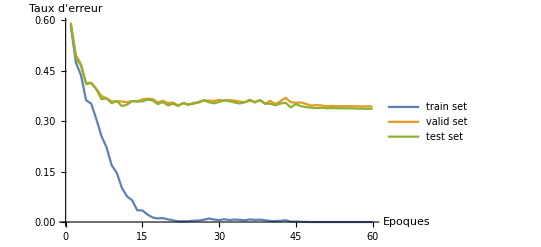

```mathematica
Print["Taux d'erreur sur test:",err3]
cerrset25={errtrain25,errvalid25,errtest25};
ListLinePlot[{errtrain25,errvalid25,errtest25},AxesLabel->{"Epoques","Taux d'erreur"},PlotLegends->{"train set","valid set","test set"}]
```

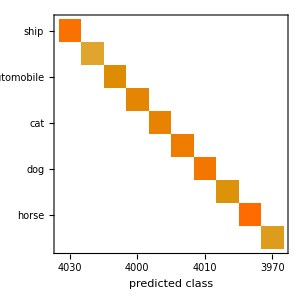
{0.,-Graphics-}

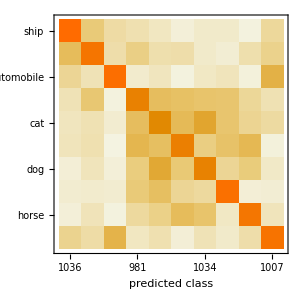
{0.3366,-Graphics-}

```mathematica
ClassifierMeasurements[cCNNtrained5,ctrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[cCNNtrained5,ctestset,{"Error","ConfusionMatrixPlot"}]
```

```mathematica
cCNNchain6=NetChain[{
ConvolutionLayer[60,{3,3}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2},"Function"-> Max], 
ConvolutionLayer[120,{3,3}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2},"Function"-> Mean], 
ConvolutionLayer[240,{3,3}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2},"Function"-> Mean], 
FlattenLayer[],
LinearLayer[800], 
ElementwiseLayer[Ramp],
LinearLayer[100],
ElementwiseLayer[Ramp],
LinearLayer[10],
SoftmaxLayer[]}, 
"Output"->NetDecoder[{"Class",{"ship","airplane","automobile","bird","cat","deer","dog","frog","horse","truck"}}],
"Input"->NetEncoder[{"Image",{32,32},"RGB"}]
]
```

NetChain[]

```mathematica
(*errtrain26={};
errvalid26={};
errtest26={};
cCNNtrained6= cCNNchain6;*)
For[i=1,i≤30,i++,
Print["Epouqe",i];
cCNNtrained6=NetTrain[cCNNtrained6,ctrainset,MaxTrainingRounds-> 1];
err1=ClassifierMeasurements[cCNNtrained6,ctrainset,{"Error"}][[1]];
errtrain26=Append[errtrain26,err1];
err2=ClassifierMeasurements[cCNNtrained6,cvalidset,{"Error"}][[1]];
errvalid26=Append[errvalid26,err2];
err3=ClassifierMeasurements[cCNNtrained6,ctestset,{"Error"}][[1]];
errtest26=Append[errtest26,err3];
Print["Taux ",err1," ",err2," ",err3];
If[err3<0.292,Break[]];
];
```

Epouqe1

Taux 0.0695 0.2954 0.2954

Epouqe2

Taux 0.047 0.2908 0.2903

Taux d'erreur sur test:0.2903

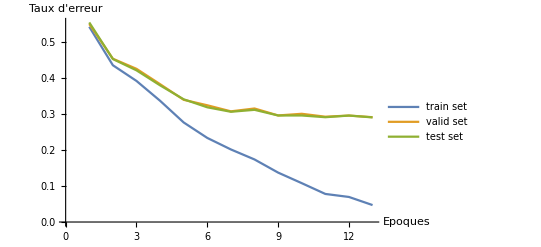

```mathematica
Print["Taux d'erreur sur test:",errtest26[[-1]]]
cerrset30={errtrain26,errvalid26,errtest26};
ListLinePlot[{errtrain26,errvalid26,errtest26},AxesLabel->{"Epoques","Taux d'erreur"},PlotLegends->{"train set","valid set","test set"}]
```

## On choisit les autres hyper-paramètres nous-même

Epouqe1

Taux 0.589425 0.5939 0.5908

Epouqe2

Taux 0.50925 0.5094 0.5129

Epouqe3

Taux 0.436825 0.4435 0.4527

Epouqe4

Taux 0.39935 0.413 0.415

Epouqe5

Taux 0.360975 0.3845 0.3886

Epouqe6

Taux 0.365975 0.3898 0.3936

Epouqe7

Taux 0.2996 0.3398 0.3406

Epouqe8

Taux 0.2857 0.3331 0.3282

Epouqe9

Taux 0.260425 0.322 0.3133

Epouqe10

Taux 0.24145 0.3116 0.3101

Epouqe11

Taux 0.219225 0.2991 0.3016

Epouqe12

Taux 0.20595 0.296 0.2961

Epouqe13

Taux 0.183675 0.2795 0.2816

Epouqe14

Taux 0.179375 0.2883 0.2968

Epouqe15

Taux 0.164075 0.2849 0.2874

Epouqe16

Taux 0.1285 0.2714 0.2738

Epouqe17

Taux 0.11605 0.2701 0.2717

Epouqe18

Taux 0.0948 0.271 0.267

Epouqe19

Taux 0.0891 0.2667 0.2723

Epouqe20

Taux 0.062375 0.2616 0.2672

Epouqe21

Taux 0.048825 0.2633 0.2648

Epouqe22

Taux 0.047775 0.2681 0.2626

Epouqe23

Taux 0.0434 0.2626 0.2676

Epouqe24

Taux 0.025825 0.2657 0.2689

Epouqe25

Taux 0.03735 0.272 0.2782

Taux d'erreur sur test:0.2782

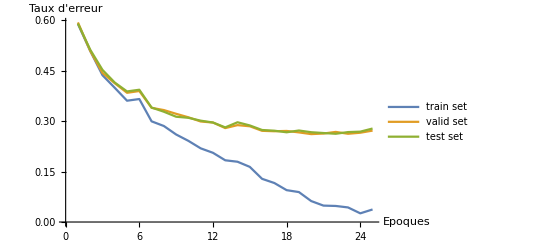

```mathematica
errtrain28={};
errvalid28={};
errtest28={};
cCNNtrained8= cCNNchain6;
For[i=1,i≤25,i++,
Print["Epouqe",i];
cCNNtrained8=NetTrain[cCNNtrained8,ctrainset,MaxTrainingRounds-> 1,BatchSize->300,Method->{"SGD","L2Regularization"->0.00000001},LearningRateMultipliers->{_->2.4}];
err1=ClassifierMeasurements[cCNNtrained8,ctrainset,{"Error"}][[1]];
errtrain28=Append[errtrain28,err1];
err2=ClassifierMeasurements[cCNNtrained8,cvalidset,{"Error"}][[1]];
errvalid28=Append[errvalid28,err2];
err3=ClassifierMeasurements[cCNNtrained8,ctestset,{"Error"}][[1]];
errtest28=Append[errtest28,err3];
Print["Taux ",err1," ",err2," ",err3];
If[err3<0.26,Break[]];
];

Print["Taux d'erreur sur test:",errtest28[[-1]]]
cerrset35={errtrain28,errvalid28,errtest28};
ListLinePlot[{errtrain28,errvalid28,errtest28},AxesLabel->{"Epoques","Taux d'erreur"},PlotLegends->{"train set","valid set","test set"}]
```

## Conclusion : 1. Le nombre de couches convolutif et la taille de les filtres convolutifs influencent la capacité de la modèle. Normalement, la taille 3 par 3 pour les filtres est meilleure que 5 par 5, et 3 couches convolutives c’est meilleur que 1 ou 2 couches. 2. La combinaison de la function pooling (max, moyenne, moyenne) est meilleur que (max, max, max).

NetChain[]

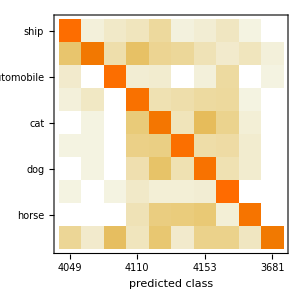
{0.03735,-Graphics-}

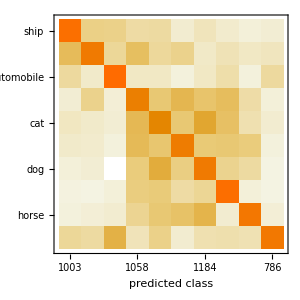
{0.2782,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cCNNtrained7=cCNNtrained8

ClassifierMeasurements[cCNNtrained7,ctrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[cCNNtrained7,ctestset,{"Error","ConfusionMatrixPlot"}]
(*"Est - ce que les examples " difficiles " et " faciles " d' une base de données sont les mêmes pour tous les algorithmes choisis?"*)
cImages=Keys[ctestset];
cEntropies=cCNNtrained7[cImages,"Entropy"];
(*choisir les images qui ont le plus haut d'entropie*)
cImages[[Ordering[cEntropies,-30]]] 
(*choisir les images qui ont le plus bas d'entropie*)
cImages[[Ordering[cEntropies,30]]]
```